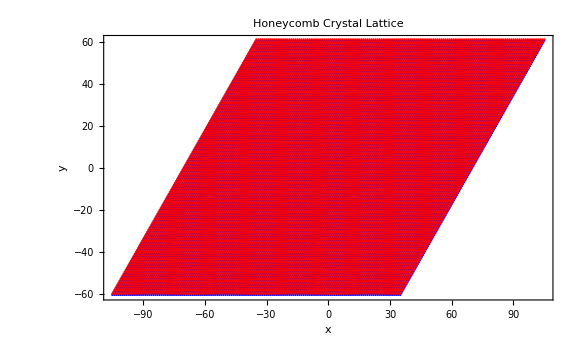

```mathematica
(* Honeycomb lattice construction - demonstration *)
(* Defining the lattice vector *)
a1={1, 0}; 
a2={1/2, (√3)/2}; 
n=10; (* Number of lattice points in each direction *)
(* generating the points in sublattices *)
sublattice1=Flatten[Table[a1*i+a2*j,{i,-n,n},{j,-n,n}],1];
sublattice2=Flatten[Table[a1*i+a2*j+{0,1/Sqrt[3]},{i,-n,n},{j,-n,n}],1];
(* combine both subblattices into single list called TriX*)
TriX = {};
Table[AppendTo[TriX,sublattice1[[i]]],{i,1,Length[sublattice1]}];
Table[AppendTo[TriX,sublattice2[[i]]],{i,1,Length[sublattice2]}];
(* Visualising the base honeycomb lattice *)
plot1 = ListPlot[sublattice1,PlotStyle->{Blue},PlotStyle->PointSize[Large]];
plot2 = ListPlot[sublattice2,PlotStyle->{Red},PlotStyle->PointSize[Large]];
Show[{plot1,plot2},
Frame->True,
FrameLabel->{"x","y"},
PlotLabel->"Honeycomb Crystal Lattice ",
 ImageSize->Large,
BaseStyle->{FontSize->15}]
```

```mathematica
(* Demonstration of triple-Q texture *)
(* Spin texture implimentation - Triple Q state of SkX*)
(* direction vectors of each spin helix in superposition *)
basisVectors ={{-1,0}, {1/2,-Sqrt[3]/2}, {1/2, Sqrt[3]/2}};(* skyrmion directions *)
size = 2; (* Size of skyrmion *)
(* Translation vectors of the skyrmions *)
T1 = {size+size/2,(√3)/2 size, 0};
T2 = {0, √3 size, 0};
T3 = {0,0,1};
(* volume and area are same as z direction is unit vector *)
volume = T1.(T2×T3); 
(* Reciprocal lattice vectors *)
B1 = (2 π)/volume(T2×T3);
B2 = (2 π)/volume(T3×T1);
(* Definitions for the spin texture *)
QVectors ={{B1[[1]],B1[[2]]}, {B2[[1]], B2[[2]]}, {B2[[1]], -B2[[2]]}};
(* Initail phase or epoch *)
epoch={Pi/3,Pi/3,Pi/3};
(* Spin texture *)
mxy [x_, y_] := Total[Table[(Sin[QVectors[[i]].{x,y}+epoch[[i]] ]) basisVectors[[i]],{i,1,3}]]
mz[x_, y_] :=  Total[Table[(Cos[QVectors[[i]].{x,y} +epoch[[i]]]),{i,1,3}]]
(* Spin texture function to get the 3D tuples *)
spins[x_, y_] := {N[mxy[x, y].{1,0}],N[ mxy[x, y].{0,1}], N[mz[x,y]]}
```

```mathematica
(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{TriX[[i]][[1]],TriX[[i]][[2]],0},{i,1,Length[TriX]}];
(* Generating the spin texture and normalizing them *)
texture =Table[spins[TriX[[i]][[1]], TriX[[i]][[2]]],{i, 1, Length[TriX]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
(* colour of the spins is according to the z component *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},
{i,1,Length[TriX] }];
cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},
{i,1,Length[TriX] }];
texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Full, Lighting->{{"Ambient",White}},ViewPoint->{0,0,1} , Background->White]
```

{198,2}

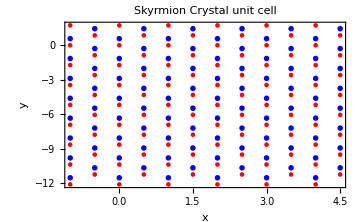

102

96

```mathematica
(* Demonstration - Isolating single skyrmion position as tuples *)
UNITcellS1={};
UNITcellS2={};

(* no. of sk in nanoribbon *)
sk = 8;
(* Bounds of unit cell *)
Xlow=-size/2;
Xhigh=(2*size)+(size/2);
Ylow=-Sqrt[3]*size*(sk-1)/2;
Yhigh=Sqrt[3]*size/2;

(* Unitcell contribution from Sublattice 1 *)
For[i = 1, i<= Length[sublattice1],i++,
If[sublattice1[[i]][[1]]>=Xlow && sublattice1[[i]][[1]]<Xhigh , 
If[sublattice1[[i]][[2]]>=Ylow && sublattice1[[i]][[2]]<=Yhigh,
AppendTo[UNITcellS1, {sublattice1[[i]][[1]], sublattice1[[i]][[2]]}]]]]
(* Unitcell contribution from Sublattice 2 *)
For[i = 1, i<= Length[sublattice2],i++,
If[sublattice2[[i]][[1]]>=Xlow && sublattice2[[i]][[1]]<Xhigh , 
If[sublattice2[[i]][[2]]>=Ylow && sublattice2[[i]][[2]]<=Yhigh,
AppendTo[UNITcellS2, {sublattice2[[i]][[1]], sublattice2[[i]][[2]]}]]]]
(* Merging them to form a single array *)
UNITcell = Flatten[{UNITcellS1, UNITcellS2}, 1];
UNITcell//Dimensions
(* Visualisint the isolated points in unit cell *)
plot3 = ListPlot[UNITcellS1,PlotStyle->{Red}];
plot4 = ListPlot[UNITcellS2,PlotStyle->{Blue}];
Show[plot3,plot4,Frame->True,PlotStyle->PointSize[0.3],FrameLabel->{"x","y"},PlotLabel->" Skyrmion Crystal unit cell ", ImageSize->Medium, BaseStyle->{FontSize->15}]
Length[UNITcellS1]
Length[UNITcellS2]
```

```mathematica
(* Visualization of the spin texture *)
(* Position vectors as 3D tuples *)
POSlist = Table[{UNITcell[[i]][[1]],UNITcell[[i]][[2]],0},{i,1,Length[UNITcell]}];
(* Generating the spin texture and normalizing them *)
list = {{ 0,Yhigh}, {1, Yhigh}, {2, Yhigh}, {-1/2, Yhigh - 1/(2Sqrt[3])},{1/2,  Yhigh - 1/(2Sqrt[3])}, {3/2,  Yhigh - 1/(2Sqrt[3])}, {5/2,  Yhigh - 1/(2Sqrt[3])},{1/2, Yhigh - 3/(2Sqrt[3])}, {3/2,  Yhigh - 3/(2Sqrt[3])},  { 0,Yhigh - 2/Sqrt[3]}, {1, Yhigh- 2/Sqrt[3]}, {2, Yhigh- 2/Sqrt[3]}, {0, Ylow}, {1, Ylow}, {2, Ylow},  {0, Ylow + 1/Sqrt[3]}, {1, Ylow+ 1/Sqrt[3]}, {2, Ylow+ 1/Sqrt[3]}, {1/2, Ylow +3/(2Sqrt[3])}, {3/2, Ylow +3/(2Sqrt[3])}, {1/2, Ylow +5/(2Sqrt[3])}, {3/2, Ylow +5/(2Sqrt[3])}};

texture =Table[spins[UNITcell[[i]][[1]], UNITcell[[i]][[2]]],{i, 1, Length[UNITcell]}]// N// Chop;
NORMtext = Table[texture[[i]]/Norm[texture[[i]]],{i,1,Length[texture]}];
(* Plotting the spin texture *)
(* colour of the spins is according to the z component *)
cylinders = Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cylinder[{POSlist[[i]]-NORMtext[[i]]/2,POSlist[[i]]},1/10]}},
{i,1,Length[UNITcell] }];
cones= Table[
{{ColorData["Rainbow"][Rescale[NORMtext[[i]][[3]],{-1,1}]],Cone[{POSlist[[i]],POSlist[[i]]+NORMtext[[i]]/2},1/5]}},
{i,1,Length[UNITcell] }];
texturePlot=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Medium, Lighting->{{"Ambient",White}},ViewPoint->{0,0,1} , Background->White]
```

-Graphics3D-

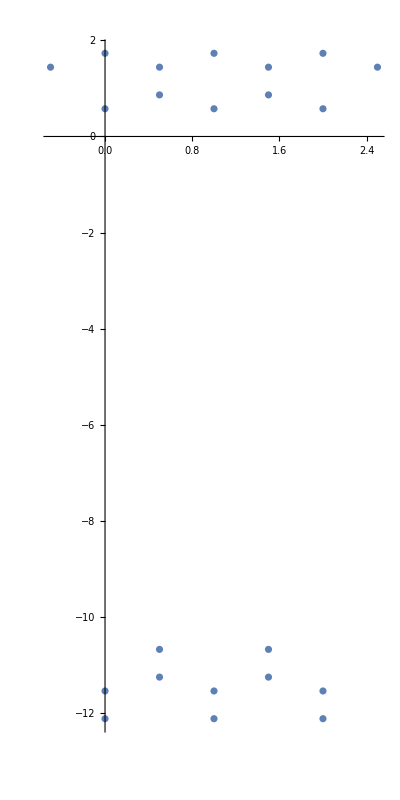

```mathematica
ListPlot[list, AspectRatio->2]
```

```mathematica
(* Neighbour table for Periodic Boundary condition Implimentation *)
Tx = {3 size, 0};
(* Convention chosen for neighbour distances "L1N1 - sub Lattice 1 Neigbour 1" *)
L1N1 = {-1/2,-1/(2 √3)};
L1N2 = {0,1/(√3)};
L1N3 = {1/2,-1/(2 √3)};
L2N1 = {-1/2,1/(2 √3)};
L2N2 = {1/2,1/(2 √3)};
L2N3 = {0,-1/(√3)};
(* Convention chosen for Array names "S1NN1 - sub Lattice 1 Nearest Neigbour 1" *)
S1NN1 ={};
S1NN2 ={};
S1NN3 ={};
S2NN1 ={};
S2NN2 ={};
S2NN3 ={};
(* SUBLATTICE 1*)
For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS2], j++,
If[UNITcellS2[[j]]==UNITcellS1[[i]]+L1N1 + {0, sk Sqrt[3] size/2} + Tx,
AppendTo[S1NN1, Null],
If[ UNITcellS2[[j]]==UNITcellS1[[i]]+L1N1 + {0, sk Sqrt[3]size/2},
AppendTo[S1NN1, Null],
If[UNITcellS2[[j]]==UNITcellS1[[i]]+L1N1 ,
AppendTo[S1NN1, j],
If[UNITcellS2[[j]] ==UNITcellS1[[i]]+L1N1+ Tx,
AppendTo[S1NN1, j]]
]]]];]

For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS2], j++,
If[UNITcellS2[[j]]==UNITcellS1[[i]]+L1N2 ,
AppendTo[S1NN2, j],
(If[UNITcellS2[[j]] ==UNITcellS1[[i]]+L1N2 - {0, sk Sqrt[3]size/2},
AppendTo[S1NN2, Null]])
]];]

For[i = 1, i<= Length[UNITcellS1], i++,
For[j=1,j<=Length[UNITcellS2], j++,
If[UNITcellS2[[j]]==UNITcellS1[[i]]+L1N3 + {0, sk Sqrt[3] size/2} - Tx,
AppendTo[S1NN3, Null],
If[ UNITcellS2[[j]]==UNITcellS1[[i]]+L1N3 + {0, sk Sqrt[3]size/2},
AppendTo[S1NN3, Null],
If[UNITcellS2[[j]]==UNITcellS1[[i]]+L1N3 ,
AppendTo[S1NN3, j],
If[UNITcellS2[[j]] ==UNITcellS1[[i]]+L1N3- Tx,
AppendTo[S1NN3, j]]
]]]];]

(* SUBLATTICE 2*)
For[i = 1, i<= Length[UNITcellS2], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcellS1[[j]]==UNITcellS2[[i]]+L2N1 ,
AppendTo[S2NN1, j],
(If[UNITcellS1[[j]] ==UNITcellS2[[i]]+L2N1+ Tx,
AppendTo[S2NN1, j]])
]];]

For[i = 1, i<= Length[UNITcellS2], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcellS1[[j]]==UNITcellS2[[i]]+L2N2 ,
AppendTo[S2NN2, j],
(If[UNITcellS1[[j]] ==UNITcellS2[[i]]+L2N2- Tx,
AppendTo[S2NN2, j]])
]];]

For[i = 1, i<= Length[UNITcellS2], i++,
For[j=1,j<=Length[UNITcellS1], j++,
If[UNITcellS1[[j]]==UNITcellS2[[i]]+L2N3 ,
AppendTo[S2NN3, j]
]];]

(* Printing the outputs *)
Length[S1NN1]
Length[S1NN2]
Length[S1NN3]
Length[S2NN1]
Length[S2NN2]
Length[S2NN3]
S2NN3
```

246

246

246

240

240

240

{2,3,5,6,7,8,10,11,12,13,14,15,17,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246}

```mathematica
(* Spin texture or spin profile in a unit cell *)
spTEXS1 = Table[spins[UNITcellS1[[i]][[1]],UNITcellS1[[i]][[2]]],{i,1, Length[UNITcellS1]}]//N//Chop;
spTEXS2 = Table[spins[UNITcellS2[[i]][[1]],UNITcellS2[[i]][[2]]],{i,1, Length[UNITcellS2]}]//N//Chop;
(* Converting to Spherical Polar Coordinates *)
SpinPOLARS1=CoordinateTransform["Cartesian"->"Spherical",spTEXS1]/.Indeterminate->0;
SpinPOLARS2=CoordinateTransform["Cartesian"->"Spherical",spTEXS2]/.Indeterminate->0;
(* Collecting the theta and phi values *)
θS1 =Table[SpinPOLARS1[[i]][[2]],{i,1, Length[UNITcellS1]}];
ϕS1 =Table[SpinPOLARS1[[i]][[3]],{i,1, Length[UNITcellS1]}];
θS2 =Table[SpinPOLARS2[[i]][[2]],{i,1, Length[UNITcellS2]}];
ϕS2 =Table[SpinPOLARS2[[i]][[3]],{i,1, Length[UNITcellS2]}];
(* spin eigen vetors *)
KetArrayS1 = Table[{Cos[1/2 θS1⟦i⟧], Sin[1/2 θS1⟦i⟧] ⅇ^(ⅈ ϕS1⟦i⟧)},{i,1, Length[UNITcellS1]}]//Chop;
KetArrayS2 = Table[{Cos[1/2 θS2⟦i⟧], Sin[1/2 θS2⟦i⟧] ⅇ^(ⅈ ϕS2⟦i⟧)},{i,1, Length[UNITcellS2]}]//Chop;
KetArrayS1// MatrixForm;
(* The conjugate vector of the spin texture |χ^↑⟩, ⟨χ^↑|:=|χ^↑⟩† *)
BraArrayS1 = Table[Conjugate[KetArrayS1[[i]]],{i,1, Length[UNITcellS1]}];
BraArrayS2 = Table[Conjugate[KetArrayS2[[i]]],{i,1, Length[UNITcellS2]}];
BraArrayS1// MatrixForm;
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

```mathematica
(* Constructing the Hamiltonian - demonstration *)
(* Parameters *)
t=1; 
(* general point in a reciprocal space *)
K[kx_] := {kx, 0}
(* Hamiltonian matrix *)
Hij[kx_]:=Module[{hopingProduct,len1,len2},len1=Length[UNITcellS1];
len2=Length[UNITcellS2];
hopingProduct=ConstantArray[0,{len1+len2,len1+len2}];
(*Fill hopingProduct for S1*)
Table[
If[S1NN1[[i]]=!=Null,
hopingProduct[[i,S1NN1[[i]]+len1]]=N[t BraArrayS1[[i]].KetArrayS2[[S1NN1[[i]]]] E^(I K[kx].L1N1)]];
If[S1NN2[[i]]=!=Null,
hopingProduct[[i,S1NN2[[i]]+len1]]=N[t BraArrayS1[[i]].KetArrayS2[[S1NN2[[i]]]] E^(I K[kx].L1N2)]];
If[S1NN3[[i]]=!=Null,
hopingProduct[[i,S1NN3[[i]]+len1]]=N[t BraArrayS1[[i]].KetArrayS2[[S1NN3[[i]]]] E^(I K[kx].L1N3)]],{i,1,len1}];

(*Fill hopingProduct for S2*)
Table[If[S2NN1[[i]]=!=Null,
hopingProduct[[i+len1,S2NN1[[i]]]]=N[t BraArrayS2[[i]].KetArrayS1[[S2NN1[[i]]]] E^(I K[kx].L2N1)]];
If[S2NN2[[i]]=!=Null,
hopingProduct[[i+len1,S2NN2[[i]]]]=N[t BraArrayS2[[i]].KetArrayS1[[S2NN2[[i]]]] E^(I K[kx].L2N2)]];
If[S2NN3[[i]]=!=Null,
hopingProduct[[i+len1,S2NN3[[i]]]]=N[t BraArrayS2[[i]].KetArrayS1[[S2NN3[[i]]]] E^(I K[kx].L2N3)]],{i,1,len2}
];

hopingProduct
]
(* Checking if the hamiltonian is hermitian *)
ConjugateTranspose[Hij[-2]]== Hij[-2]
```

True

```mathematica
(* Demonstration - band structure plot *)
Ev[kx_] := Sort[Eigenvalues[Hij[kx]]]
BZ = Table[i, {i, -Pi/Tx[[1]], Pi/Tx[[1]], 2 Pi/(Tx[[1]] 50)}];
bands[n_] := Table[Ev[BZ[[i]]][[n]], {i, 1, Length[BZ]}]
data = Table[bands[i], {i, 1, Length[UNITcellS1] + Length[UNITcellS2]}];
```

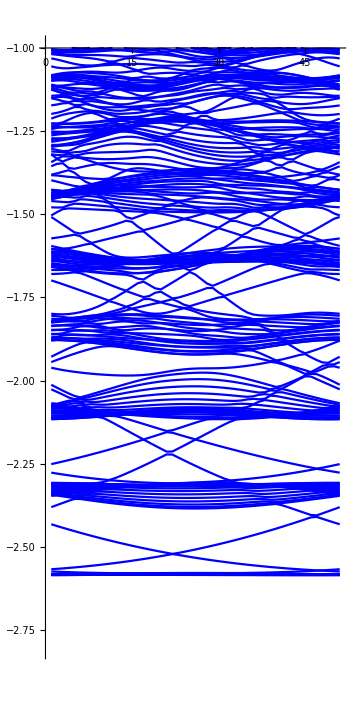

```mathematica
ListLinePlot[data,PlotStyle->{Blue},ImageSize->Medium,PlotRange->{{Automatic,Automatic},{-2.8,-1}},AspectRatio->2]
```